# 20 Gaussian Elimination: LU Decomposition

We know how to solve triangular systems of equations.  We are going to see how to reduce a general system 
	A.x=b 
to two triangular systems.

### Simple Matrices

What does the matrix below do?

```mathematica
L3=IdentityMatrix[8]; L3⟦4;;8,3⟧={L43,L53,L63,L73,L83};
MatrixForm[L3]
```

(1 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 1 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 1 | 0 | 0 | 0 | 0 | 0
0 | 0 | L43 | 1 | 0 | 0 | 0 | 0
0 | 0 | L53 | 0 | 1 | 0 | 0 | 0
0 | 0 | L63 | 0 | 0 | 1 | 0 | 0
0 | 0 | L73 | 0 | 0 | 0 | 1 | 0
0 | 0 | L83 | 0 | 0 | 0 | 0 | 1)

Can you just write down its inverse?

```mathematica
MatrixForm[Inverse[L3]]
```

### Multiplying Simple Matrices

Here is another “similar” matrix

```mathematica
L4=IdentityMatrix[8]; L4⟦5;;8,4⟧={L54,L64,L74,L84};
MatrixForm[L4]
```

(1 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 1 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 1 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 1 | 0 | 0 | 0 | 0
0 | 0 | 0 | L54 | 1 | 0 | 0 | 0
0 | 0 | 0 | L64 | 0 | 1 | 0 | 0
0 | 0 | 0 | L74 | 0 | 0 | 1 | 0
0 | 0 | 0 | L84 | 0 | 0 | 0 | 1)

The product L3.L4 is simple

```mathematica
MatrixForm[L3.L4]
```

(1 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 1 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 1 | 0 | 0 | 0 | 0 | 0
0 | 0 | L43 | 1 | 0 | 0 | 0 | 0
0 | 0 | L53 | L54 | 1 | 0 | 0 | 0
0 | 0 | L63 | L64 | 0 | 1 | 0 | 0
0 | 0 | L73 | L74 | 0 | 0 | 1 | 0
0 | 0 | L83 | L84 | 0 | 0 | 0 | 1)

However, the product L4.L3 is not. To use these matrices we need to work our way down.

```mathematica
MatrixForm[L4.L3]
```

(1 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 1 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 1 | 0 | 0 | 0 | 0 | 0
0 | 0 | L43 | 1 | 0 | 0 | 0 | 0
0 | 0 | L53+L43 L54 | L54 | 1 | 0 | 0 | 0
0 | 0 | L63+L43 L64 | L64 | 0 | 1 | 0 | 0
0 | 0 | L73+L43 L74 | L74 | 0 | 0 | 1 | 0
0 | 0 | L83+L43 L84 | L84 | 0 | 0 | 0 | 1)

### Chaining Simple Matrices

```mathematica
Clear[L]
MatrixForm[
Mat=LowerTriangularize[Table[StringForm["L````",i,j],{i,8},{j,8}],-1]+IdentityMatrix[8]
]
```

The lower triangular matrix below is the product of 7 of these simple matrices.

```mathematica
Clear[L]
MatrixForm[
Mat=LowerTriangularize[Table[StringForm["L````",i,j],{i,8},{j,8}],-1]+IdentityMatrix[8]
]
```

(1 | 0 | 0 | 0 | 0 | 0 | 0 | 0
L21 | 1 | 0 | 0 | 0 | 0 | 0 | 0
L31 | L32 | 1 | 0 | 0 | 0 | 0 | 0
L41 | L42 | L43 | 1 | 0 | 0 | 0 | 0
L51 | L52 | L53 | L54 | 1 | 0 | 0 | 0
L61 | L62 | L63 | L64 | L65 | 1 | 0 | 0
L71 | L72 | L73 | L74 | L75 | L76 | 1 | 0
L81 | L82 | L83 | L84 | L85 | L86 | L87 | 1)

## Using these Simple Matrices to Create Zeros

### Manually

Gaussian Elimination is the first way people worked out to make zeros. Note, if you were solving equations by candle light in 18XX you would not organize it this way!

```mathematica
m=8;
A0=RandomReal[{-1,1},{m,m}];
L1=IdentityMatrix[m]; L1⟦2;;m,1⟧=A0⟦2;;m,1⟧/A0⟦1,1⟧;
MatrixForm[A1 = Chop[Inverse[L1].A0]]
```

(-0.966963 | 0.290369 | -0.0262626 | -0.241985 | -0.491152 | 0.31337 | -0.468101 | 0.373045
0 | 0.283374 | 0.920118 | -0.234771 | -0.501193 | 0.117755 | -1.00874 | 0.70277
0 | -0.353152 | 0.249303 | 0.48495 | -0.28378 | -0.0796965 | -0.268545 | 0.50265
0 | -0.341409 | 0.435038 | 1.10759 | -0.322115 | 0.430604 | 1.07313 | -0.0842826
0 | 0.760714 | -0.000799199 | -0.42559 | -0.560581 | 0.575804 | 0.0853222 | -0.0330477
0 | -0.303617 | 0.0899803 | -0.738744 | 0.587482 | 0.632003 | -0.983913 | -0.736503
0 | -0.700555 | -0.182778 | -0.300292 | 1.00375 | -1.09079 | -0.3428 | 0.546039
0 | 0.0868441 | 0.0368254 | 0.404099 | 0.631724 | 0.945893 | 0.630143 | -0.397883)

If we do it again we can make another almost column of zeros.

```mathematica
L2=IdentityMatrix[m]; L2⟦3;;m,2⟧=A1⟦3;;m,2⟧/A1⟦2,2⟧;
MatrixForm[A2 = Chop[Inverse[L2].A1]]
```

(0.916222 | 0.889423 | 0.907701 | 0.177721 | 0.163032 | 0.521225 | -0.280206 | 0.94551
0 | -1.28804 | -0.00343107 | 0.538521 | -1.03772 | 0.160713 | 0.17824 | -0.717724
0 | 0 | -0.80234 | -1.1965 | 0.0571537 | 0.0682028 | 0.428189 | -0.0594425
0 | 0 | -0.115802 | -0.859947 | 0.944826 | -0.230825 | 0.160214 | 0.379703
0 | 0 | 0.984991 | 0.487879 | -1.18531 | 0.884908 | -0.874171 | 0.0836534
0 | 0 | -0.505989 | -0.883584 | 1.21078 | 0.989855 | -0.39046 | -0.208784
0 | 0 | 0.772833 | 0.225173 | 1.44135 | -0.550338 | 0.360345 | 0.812919
0 | 0 | -1.15809 | 0.564642 | -0.312047 | -0.459696 | 0.635607 | -0.63985)

We can keep going.

```mathematica
L3=IdentityMatrix[m]; L3⟦4;;m,3⟧=A2⟦4;;m,3⟧/A2⟦3,3⟧;
MatrixForm[A3 = Chop[Inverse[L3].A2]]
L4=IdentityMatrix[m]; L4⟦5;;m,4⟧=A3⟦5;;m,4⟧/A3⟦4,4⟧;
MatrixForm[A4 = Chop[Inverse[L4].A3]]
L5=IdentityMatrix[m]; L5⟦6;;m,5⟧=A4⟦6;;m,5⟧/A4⟦5,5⟧;
MatrixForm[A5 = Chop[Inverse[L5].A4]]
L6=IdentityMatrix[m]; L6⟦7;;m,6⟧=A5⟦7;;m,6⟧/A5⟦6,6⟧;
MatrixForm[A6 = Chop[Inverse[L6].A5]]
L7=IdentityMatrix[m]; L7⟦8;;m,7⟧=A6⟦8;;m,7⟧/A6⟦7,7⟧;
MatrixForm[A7 = Chop[Inverse[L7].A6]]
```

(0.916222 | 0.889423 | 0.907701 | 0.177721 | 0.163032 | 0.521225 | -0.280206 | 0.94551
0 | -1.28804 | -0.00343107 | 0.538521 | -1.03772 | 0.160713 | 0.17824 | -0.717724
0 | 0 | -0.80234 | -1.1965 | 0.0571537 | 0.0682028 | 0.428189 | -0.0594425
0 | 0 | 0 | -0.687256 | 0.936577 | -0.240669 | 0.0984137 | 0.388282
0 | 0 | 0 | -0.981001 | -1.11515 | 0.968637 | -0.348505 | 0.0106789
0 | 0 | 0 | -0.129022 | 1.17474 | 0.946843 | -0.660494 | -0.171297
0 | 0 | 0 | -0.927324 | 1.49641 | -0.484643 | 0.772787 | 0.755663
0 | 0 | 0 | 2.29166 | -0.394542 | -0.558139 | 0.0175628 | -0.554052)

(0.916222 | 0.889423 | 0.907701 | 0.177721 | 0.163032 | 0.521225 | -0.280206 | 0.94551
0 | -1.28804 | -0.00343107 | 0.538521 | -1.03772 | 0.160713 | 0.17824 | -0.717724
0 | 0 | -0.80234 | -1.1965 | 0.0571537 | 0.0682028 | 0.428189 | -0.0594425
0 | 0 | 0 | -0.687256 | 0.936577 | -0.240669 | 0.0984137 | 0.388282
0 | 0 | 0 | 0 | -2.45203 | 1.31217 | -0.488982 | -0.543562
0 | 0 | 0 | 0 | 0.99891 | 0.992025 | -0.67897 | -0.244192
0 | 0 | 0 | 0 | 0.23267 | -0.159905 | 0.639996 | 0.231748
0 | 0 | 0 | 0 | 2.72848 | -1.36065 | 0.345724 | 0.740678)

(0.916222 | 0.889423 | 0.907701 | 0.177721 | 0.163032 | 0.521225 | -0.280206 | 0.94551
0 | -1.28804 | -0.00343107 | 0.538521 | -1.03772 | 0.160713 | 0.17824 | -0.717724
0 | 0 | -0.80234 | -1.1965 | 0.0571537 | 0.0682028 | 0.428189 | -0.0594425
0 | 0 | 0 | -0.687256 | 0.936577 | -0.240669 | 0.0984137 | 0.388282
0 | 0 | 0 | 0 | -2.45203 | 1.31217 | -0.488982 | -0.543562
0 | 0 | 0 | 0 | 0 | 1.52658 | -0.878172 | -0.465628
0 | 0 | 0 | 0 | 0 | -0.035395 | 0.593597 | 0.18017
0 | 0 | 0 | 0 | 0 | 0.0994577 | -0.198387 | 0.135834)

(0.916222 | 0.889423 | 0.907701 | 0.177721 | 0.163032 | 0.521225 | -0.280206 | 0.94551
0 | -1.28804 | -0.00343107 | 0.538521 | -1.03772 | 0.160713 | 0.17824 | -0.717724
0 | 0 | -0.80234 | -1.1965 | 0.0571537 | 0.0682028 | 0.428189 | -0.0594425
0 | 0 | 0 | -0.687256 | 0.936577 | -0.240669 | 0.0984137 | 0.388282
0 | 0 | 0 | 0 | -2.45203 | 1.31217 | -0.488982 | -0.543562
0 | 0 | 0 | 0 | 0 | 1.52658 | -0.878172 | -0.465628
0 | 0 | 0 | 0 | 0 | 0 | 0.573236 | 0.169374
0 | 0 | 0 | 0 | 0 | 0 | -0.141174 | 0.16617)

(0.916222 | 0.889423 | 0.907701 | 0.177721 | 0.163032 | 0.521225 | -0.280206 | 0.94551
0 | -1.28804 | -0.00343107 | 0.538521 | -1.03772 | 0.160713 | 0.17824 | -0.717724
0 | 0 | -0.80234 | -1.1965 | 0.0571537 | 0.0682028 | 0.428189 | -0.0594425
0 | 0 | 0 | -0.687256 | 0.936577 | -0.240669 | 0.0984137 | 0.388282
0 | 0 | 0 | 0 | -2.45203 | 1.31217 | -0.488982 | -0.543562
0 | 0 | 0 | 0 | 0 | 1.52658 | -0.878172 | -0.465628
0 | 0 | 0 | 0 | 0 | 0 | 0.573236 | 0.169374
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0.207882)

### Script

All this typing is nuts.  All the L entries can be stored in the same place.  We can recycle the storage for the matrix that winds up being U (the things called A0, A1, …) up above.  Finally, since only a few rows of the matrix are changed at a time changed at a time we might as well do only those rows

2.37782×10^-15

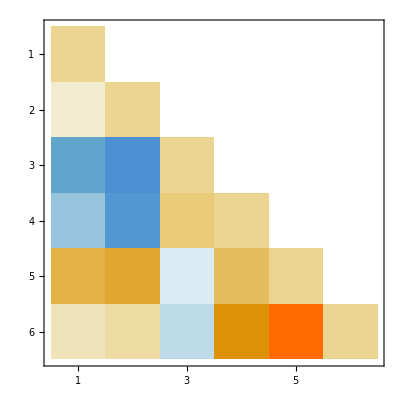
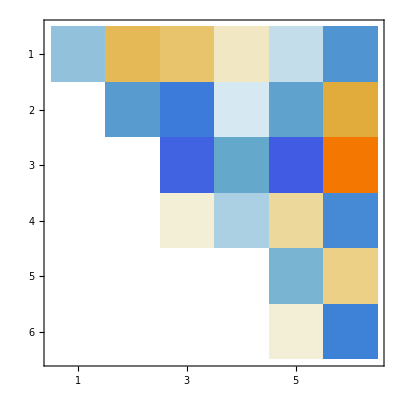

```mathematica
m=6;
A=RandomReal[{-1,1},{m,m}];
(* Start Script *)
L=IdentityMatrix[m];
U=A; 
Do[
Do[
L⟦j,k⟧=U⟦j,k⟧/U⟦k,k⟧;
U⟦j,k;;m⟧-=L⟦j,k⟧ U⟦k,k;;m⟧,
{j,k+1,m}],
{k,1,m-1}]
Norm[A-L.U]
Map[MatrixPlot,{L,U}]
```

### Function

4.70017×10^-12

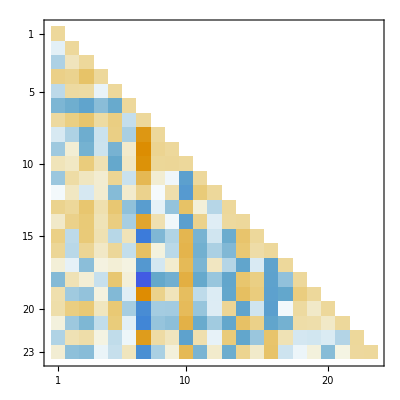
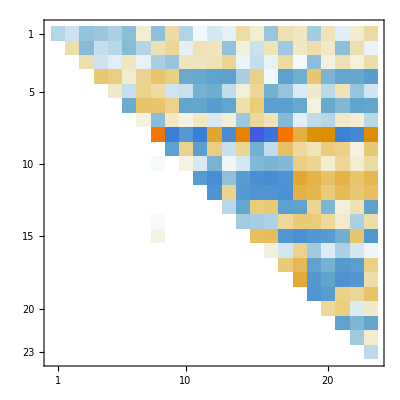

```mathematica
MyLUDecomposition[A_]:= Module[{m=Length[A],L,U=A},
(* Start Script *)
L=IdentityMatrix[m];
Do[
Do[
L⟦j,k⟧=U⟦j,k⟧/U⟦k,k⟧;
U⟦j,k;;m⟧-=L⟦j,k⟧ U⟦k,k;;m⟧,
{j,k+1,m}],
{k,1,m-1}];
{L,U}
]

m=23;
A=RandomReal[{-1,1},{m,m}];
{L,U}=MyLUDecomposition[A];
Norm[A-L.U]
Map[MatrixPlot,{L,U}]
```

## Solving a Linear System with an LU Decomposition

We know how to solve triangular systems. we even know that the obvious algorithm is backwards stable. We now know how to split a matrix up into two triangular matrices A=L.U.  we should be able to put this together to get an algorithm to solve A.x=L.U.x=b. All we need to do is make up an intermediate variable.  y=U.x 
	L.(U.x)=L.y=b
Solve L.y=b to get a ỹ.  Then solve U.x=ỹ to get x̃.  Since the triangular solves are backwards stable this would all be great if the L.U decomposition was stable!  It is not!

### Need for Pivoting

There are perfectly well behaved linear systems which will break our first attempt at an LU decomposition.  For example
	(ϵ | 1.0
1.0 | 1.0).(x1
x2)=(b1
b2).
In exact arithmetic Gaussian elimination gives the solution
	x1 | = | (b1-b2)/(-1+ϵ) | ⟶ | b2-b1
x2 | = | (-b1+b2 ϵ)/(-1+ϵ) | ⟶ | b1
The system is fine as ϵ→0.  Our first attempt at an LU decomposition gives. 
	A=(ϵ | 1.0
1.0 | 1.0)=(1 | 0
ϵ^-1 | 1)(ϵ | 1.0
0 | 1-ϵ^-1)
which in exact arithmetic works just fine: exact arithmetic does not care that ϵ^-1 could be huge. On any computer this is a real problem!  When ϵ is small in floating point the last entry gets messed up and we will get 
	 (1 | 0
ϵ^-1 | 1)(ϵ | 1.0
0 | -ϵ^-1)=(ϵ | 1
1 | 0)

The sad thing is this has nothing to do with the equations/matrix. As ϵ→0 the condition number κ(A) is the singular value ratio of ratio of (0 | 1.0
1.0 | 1.0) which is roughly 3.

The really sad thing is that if we had just written down the equations in a different order we would have got (1.0 | 1.0
ϵ | 1.0)=(1 | 0
ϵ | 1)(1 | 1
0 | 1-ϵ) which would have worked just fine.

We can not write a usage guide for a function that says “make sure your equations are in a decent order”. We need to make an algorithm that reorders the equations (rows in the matrix) into a good order on the fly.

The first question is given a matrix A which row (same as equation) should we start with.

After the first row we just ask which of the remaining rows is best to do next.

The resulting algorithm is called an LU decomposition with row pivoting.

You can also ask which remaining variable (column of the matrix would be best) which gives column pivoting.

If you ask which is the best variable and equation you are doing complete pivoting!